# Hw 6 - Complex Variables

## Page 237 visualize curvature

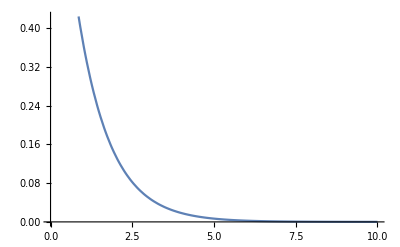

```mathematica
Plot[E^-x,{x,0,10}]
```

## 3 ii - done using calculations

### First assign Φ to the expression

```mathematica
Clear[Φ]
Φ=E^(x^2-y^2)Cos[2x y]
```

ⅇ^(x^2-y^2) Cos[2 x y]

### Add together the second partial derivatives

```mathematica
D[Φ,{x,2}]+D[Φ,{y,2}]
```

-4 ⅇ^(x^2-y^2) x^2 Cos[2 x y]+(2 ⅇ^(x^2-y^2)+4 ⅇ^(x^2-y^2) x^2) Cos[2 x y]-4 ⅇ^(x^2-y^2) y^2 Cos[2 x y]+(-2 ⅇ^(x^2-y^2)+4 ⅇ^(x^2-y^2) y^2) Cos[2 x y]

### Simplify the previous output. In this case, it simplifies to zero.

```mathematica
Simplify[%]
```

0